```mathematica
SetDirectory[$UserDocumentsDirectory];
SetDirectory[".\\Research\\current sims"];
paints=Delete[ColorData[58,"ColorList"],{{7},{13},{14}}];
gammadirs =Sort@FileNames["Gamma*"]
fitPick = {"Sinc", "Sinc","Sinc"};
labls = {"γ(1, 30)", "γ(4, 12)", "γ(9, 5)"} ;
params = {{1,30}, {4,12},{9,5}};
(*Must keep same pdf order everywhere*)
rules= Outer[Import[Last[Sort[FileNames[".\\"<>gammadirs⟦#⟧<>"\\"<>fitPick⟦#⟧<>"\\*.par"], (AbsoluteTime@FileDate@#1<AbsoluteTime@FileDate@#2)& ]
], "Table"]&,{1,2,3}];
rules//Dimensions
```

{Gamma1-1,30,Gamma2-4,12,Gamma3-9,5}

{3,15,4}

```mathematica
setSAMS = {Sinc[(#1-#2)/#3]&, Exp[-((#1-#2)/#3)^2]&,Piecewise[{{1-Abs[#1-#2]/#3,Abs[#1-#2]≤#3}}]&,(1+((#1-#2)/#3)^2)^-1&,Exp[-Abs[((#1-#2)/#3)]]&,1+Tanh[-((#1-#2)/#3)^2]&};
aj= setSAMS⟦1⟧;
r=Length@rules⟦1,All⟧;
den[θ_, i:(1|2|3)]:=∑_(k=1)^r rules⟦i,k,4⟧×aj[θ, rules⟦i,k,1⟧,rules⟦i,k,2⟧]
fuzzyPrior[θ_, i:(1|2|3)]:= Piecewise[{{∑_(j=1)^r (aj[θ, rules⟦i,j,1⟧,rules⟦i,j,2⟧]×rules⟦i,j,3⟧×rules⟦i,j,4⟧)/den[θ,i], 0<θ≤150}}]
```

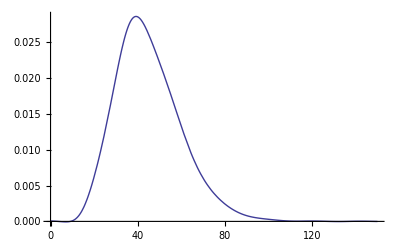

```mathematica
Plot[fuzzyPrior[θ,3], {θ,0,150}]
```